```mathematica
3. domača naloga
```

```mathematica
1. naloga
```

```mathematica
v0={10,3};
GG=9.81;
H=10;
a = {0, -GG};
x0 ={0, H}
```

{0,10}

```mathematica
v(t)=Subscript[v, 0] + at
x(t)=Subscript[x, 0] + Subscript[v, 0] * t + (a * t^2)/2
```

at+v_0

{t v_0+x_0,-4.905 t^2+t v_0+x_0}

```mathematica
v[t_] := {v0[[1]], v0[[2]] - GG*t}
```

```mathematica
{v0[[1]], v0[[2]] - GG*t}
v0 + a*t
```

{10,3-9.81 t}

{10,3-9.81 t}

```mathematica
v[t_] := v0 + a*t
X[t_] := x0 + v0*t + a*t^2/2
```

```mathematica
Čas doseganja najvišje višine leta
```

```mathematica
t = (v0 * Sinα)/GG
```

{1.01937 Sinα,0.30581 Sinα}

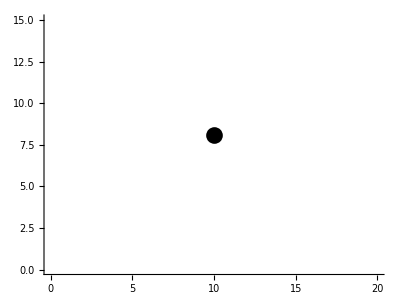

```mathematica
SlikaTocke[t_] := {PointSize[0.03], Point[X[t]]};
Graphics[SlikaTocke[1], Axes-> True, PlotRange-> {{0, 20}, {0, 15}}]
```

```mathematica
Manipulate[GraphicsGrid[SlikaTocke[t], Axes-> True, PlotRange-> {{0, 20}, {0, 15}}], {t, 0, 3}]
```

```mathematica
Manipulate[Graphics[{SlikaTocke[t], Arrow[{{1, 1}, {2, 2}}]}, Axes-> True, PlotRange-> {{0, 20}, {0, 15}}], {t, 0, 3}
```

```mathematica
DH = (v0[[1]]^2 + v0[[2]]^2)^(1/2)
SK = v0[[2]]/ DH //N
NT = DH^2 * SK^2 / (2*GG) + H
```

√109

0.287348

10.4587

```mathematica
casLetaDoTemena = 2 * DH * SK/(GG * 2)
domet = DH^2 * Sin[2*ArcSin[SK]]/GG + H
```

0.30581

16.1162

```mathematica
casLeta = casLetaDoTemena * 2 + (2*H/GG)^(1/2)
```

2.03946

```mathematica
2. naloga
```

```mathematica
r111 = Ravnina[{-1, -1, -1}, {1, 1, 1}]
```

Ravnina[{-1,-1,-1},{1,1,1}]

```mathematica
Slika[Ravnina[n_, v_]] := Hyperplane[n, v]
Format[r_Ravnina] := Graphics3D[Slika[r]]
r111
```

-Graphics3D-

```mathematica
rx = Ravnina[{1, 0, 0}, {0, 0, 0}];
ry = Ravnina[{0, 1, 0}, {0, 0, 0}];
rz = Ravnina[{0, 0, 1}, {0, 0, 0}];
r111 = Ravnina[{-1, -1, -1}, {1, 1, 1}];
SlikaNormale[Ravnina[n_, v_]] := Arrow[{v, v + n}]
Graphics3D[{Slika[r111], SlikaNormale[r111]}]
ravnine = {rx, ry, rz, r111}
```

-Graphics3D-

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
obeSliki[r_Ravnina] := {Slika[r], SlikaNormale[r]}
Graphics3D[Map[obeSliki, ravnine]]
```

{-Graphics3D-,-Graphics3D-}

-Graphics3D-

```mathematica
Graphics3D[Map[{Slika[#], SlikaNormale[#]}&, ravnine]]
```

-Graphics3D-

```mathematica
rx = Ravnina[{1, 0, 0}, {0, 0, 0}];
ry = Ravnina[{0, 1, 0},{0, 0, 0}];
rz = Ravnina[{0, 0, 1}, {0, 0, 0}];
r111 = Ravnina[{-1, -1, -1}, {1, 1, 1}]
ravnine = {rx, ry, rz, r111}
SlikaNormale[Ravnina[n_, v_]] := Arrow[{v, v + n}]
Slika[Ravnina[n_, v_]] := Hyperplane[n, v]
slikeRavnin = Map[Slika, ravnine];
Graphics3D[{slikeRavnin},
PlotRange-> {{-1, 4}, {-1, 4}, {-1, 4}}]
```

-Graphics3D-

```mathematica
EnacbaRavnine[Ravnina[n_, r_]] := Module[{x, y, z,levi, desni},
levi = (n[[1]])*x + (n[[2]])*y + (n[[3]])*z;
desni = n[[1]]*r[[1]] + n[[2]]*r[[2]] + n[[3]]*r[[3]];
Return levi = desni]
EnacbaRavnine[r111]
```

-3

```mathematica
3. naloga
```

```mathematica
t1 = {1, 2, 4}
t2 = {4, 5, 9}
t3= {6, 6, 7}
t4 = {4, 1, 4}
```

{1,2,4}

{4,5,9}

{6,6,7}

{4,1,4}

```mathematica
baza= {t1, t2, t3, t4}
```

{{1,2,4},{4,5,9},{6,6,7},{4,1,4}}

```mathematica
Graphics3D[Parallelepiped[t1, {t2, t3, t4}]]
```

-Graphics3D-